# Predicting numerical variables and sequences

## Predict insurance costs

This exercise is taken from Lantz’s book “Machine Learning with R”

In order for a health insurance company to make money, it needs to collect more in yearly premiums than it spends on medical care to its beneficiaries. As a result, insurers invest a great deal of time and money in developing models that accurately forecast medical expenses for the insured population.

Medical expenses are difficult to estimate because the most costly conditions are rare and seemingly random. Still, some conditions are more prevalent for certain segments of the population. For instance, lung cancer is more likely among smokers than non-smokers, and heart disease may be more likely among the obese.

The goal of this analysis is to use patient data to estimate the average medical care expenses for such population segments. These estimates can be used to create actuarial tables that set the price of yearly premiums higher or lower, depending on the expected treatment costs.

### The data

The data set is available in csv format from MyAberdeen. It consists of 7 columns with the following information:

age: age of primary beneficiary

sex: insurance contractor gender, female, male

bmi: Body mass index, providing an understanding of body, weights that are relatively high or low relative to height, objective index of body weight (kg / m^2) using the ratio of height to weight, ideally 18.5 to 24.9

children: Number of children covered by health insurance / Number of dependents

smoker: yes/no

region: the beneficiary's residential area in the US, northeast, southeast, southwest, northwest.

charges: Individual medical costs billed by health insurance

Goal of the analysis: We will assume that the dependent variable is charges, i.e. we intend to use the other variables to predict the individual medical costs billed by health insurance.

### Task 1

Download the data from MyAberdeen and import to a variable named data

```mathematica
data = SemanticImport["C:\\Users\\spano\\Downloads\\insurance.csv"]
```

Dataset[<>]

### Task 2

Look at the first 5 rows of the data.

```mathematica
Take[data[[1 ;; 5, All]]]
```

### Task 3

In the previous task you would have realised that the first row of the dataset is different to the rest since it gives the name of the columns, i.e. it defines the names of the features. Separate the name of the features (first row) from the list of features for each beneficiary (drop the first row). Proceed as follows:

Define a list named features containing the name of the features given in the first row.

```mathematica
?First
```

```mathematica
features = First@Keys@data // Normal;
```

Define a list named insurance containing all rows in data except the first

```mathematica
insurance = Values@data // Normal;
```

```mathematica
bmi =insurance[[All,3]];
```

### Task 4

Use the insurance list to extract the dependent variable. Store the values of the dependent variable in a new list called charges.

```mathematica
charges = insurance[[All, 7]];
```

### Task 5

Plot a histogram of charges.

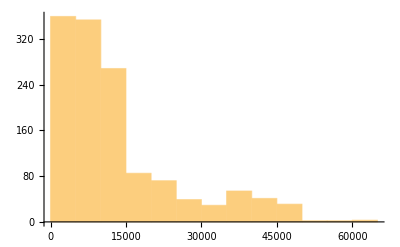

```mathematica
Histogram[charges]
```

### Task 6

Show that there are 662 female and 676 male individuals in the dataset.

```mathematica
sex = {"male", "female"};
```

```mathematica
showsex =Cases[insurance,{___, #, ___}] &/@ sex;
```

```mathematica
showsex[[1]] // Length;
```

```mathematica
showsex[[2]] // Length;
```

```mathematica
(*second method*)
```

```mathematica
numbergender = data[[All, 2]] ;
```

```mathematica
Counts@numbergender
```

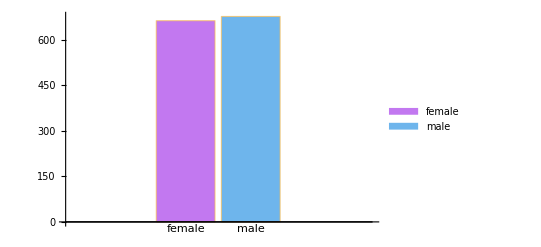

```mathematica
BarChart[Counts@numbergender, ChartLabels->{"female", "male"}, ChartLegends->Automatic, ChartStyle->"Pastel"]
```

### Task 7

Use a scatter plot to analyse the relation between the cost billed and age. Comment on the results. In particular, do you think that age is enough to explain the billed costs?

```mathematica
age = insurance[[All, 1]];
```

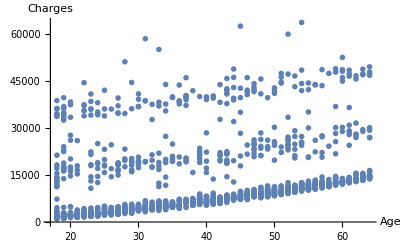

```mathematica
ListPlot[Transpose@{insurance[[All, 1]], insurance[[All, 7]]}, AxesLabel->{"Age", "Charges"},  PlotMarkers->{"OpenMarkers", Medium}, PlotRange->All]
```

```mathematica
ageclusters = FindClusters[Transpose@{insurance[[All, 1]], insurance[[All, 7]]}, 3, Method->"KMeans"];
```

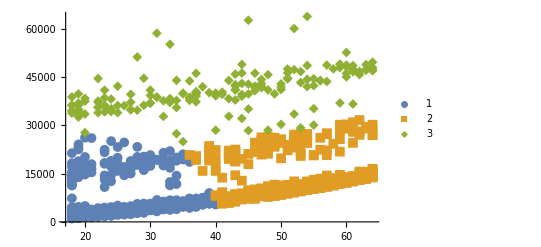

```mathematica
ListPlot[ageclusters, PlotLegends->Automatic, PlotMarkers->{Automatic, Medium}]
```

### Task 8

How is the cost related to bmi? Discuss the result.

```mathematica
bmiclusters = FindClusters[Transpose@{insurance[[All, 3]], insurance[[All, 7]]}, 2, Method->"KMeans"];
```

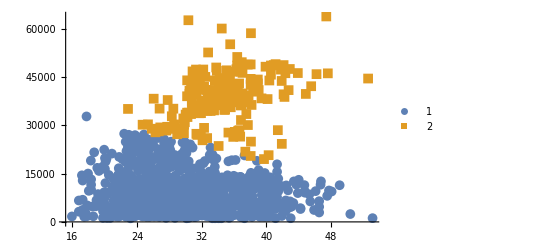

```mathematica
ListPlot[bmiclusters, PlotLegends->Automatic, PlotMarkers->{Automatic, Medium}]
```

### Task 9

How is the cost related to the number of children?

```mathematica
childrenclusters = FindClusters[Transpose@{insurance[[All, 4]], insurance[[All, 7]]}, 1, Method->"KMeans"];
```

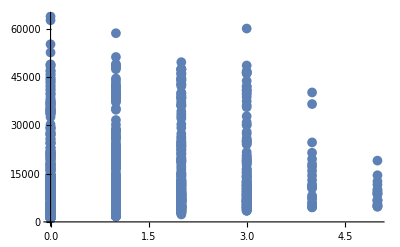

```mathematica
ListPlot[childrenclusters, PlotLegends->Automatic, PlotMarkers->{Automatic, Medium}]
```

### Task 10

Show that the mean charge for smokers is 32050.2 whereas it is 8434.3 for non-smokers

```mathematica
describe[list_List] := {{"Count", Length[list]}, {"Mean", Mean[list]}, {"Standard Deviation", StandardDeviation[list]}, {"Minimum", Min[list], "25%", Quantile[list, 0.25]}, {"50%", Quantile[list, 0.5]}, {"75%", Quantile[list, 0.75]}, {"Maximum", Max[list]}}
```

```mathematica
data[GroupBy["smoker"], describe, "charges"]
```

### Task 11

Define a training dataset (named trainingdata) as a random sample of 1/3 of the elements in the original data. Define a test dataset (named testdata) corresponding to the complement of the training dataset.

```mathematica
α = Length[data]
```

1338

```mathematica
trainDim = Floor[α/3]
```

446

```mathematica
{datatrain, datatest} = TakeDrop[RandomSample@Values@data // Normal, trainDim];
```

```mathematica
Dimensions[datatrain]
```

{446,7}

```mathematica
Dimensions[datatest]
```

{892,7}

```mathematica
training = datatrain[[All,1;; 6]];
```

```mathematica
traininganswer = datatrain[[All, 7]];
```

```mathematica
testing = datatest[[All,1;; 6]];
```

```mathematica
testinganswer = datatest[[All, 7]];
```

```mathematica
trainingdata = Table[training[[i]] -> traininganswer[[i]], {i, Length[training]}];
```

```mathematica
testingdata = Table[testing[[i]] -> testinganswer[[i]], {i, Length[testing]}];
```

### Task 12

Use the training dataset to train a predictor

```mathematica
insurancepredictor = Predict[trainingdata, TargetDevice->"GPU"]
```

PredictorFunction[…]

### Task 13

Create a predictor measurements object (named insurancepm)to analyse the performance of the trained model on the test data.

```mathematica
insuranceperformance = PredictorMeasurements[insurancepredictor, testingdata]
```

PredictorMeasurementsObject[…]

### Task 14

Look at the properties of the insurancepm.

```mathematica
Manipulate[insuranceperformance[prop], {prop, insuranceperformance["Properties"]}, SaveDefinitions->True]
```

### Task 15

Get an estimate of the typical error of predictions in terms of their standard deviation and a histogram of residuals. Draw a comparison plot and comment on the results.

```mathematica
Manipulate[insuranceperformance[prop], {prop, insuranceperformance["Properties"]}, SaveDefinitions->True];
```

```mathematica
predictorcomparison = Dataset@ReverseSort@AssociationMap[PredictorMeasurements[Predict[trainingdata, Method->#], testingdata, {"RSquared", "StandardDeviation"}]&, {"RandomForest", "NearestNeighbors", "LinearRegression", "GradientBoostedTrees", "DecisionTree", "NeuralNetwork", "Gaussianprocess"}];
```

Predict::elmntavsl: "Gaussianprocess" is not an available method. Did you mean "GaussianProcess" instead? Possible methods also include "DecisionTree", "GradientBoostedTrees", "LinearRegression", "NearestNeighbors", "NeuralNetwork", "RandomForest", and Automatic.

PredictorMeasurements::wrgfunc: The first argument should be a PredictorFunction instead of Predict[{{19,male,29.07,0,yes,northwest}→17352.7,{26,female,40.185,0,no,northwest}→3201.25,{18,female,28.215,0,no,northeast}→2200.83,{39,female,24.225,5,no,northwest}→8965.8,{64,female,26.885,0,yes,northwest}→29331.,«41»,{19,female,28.4,1,no,southwest}→2331.52,{46,male,40.375,2,no,northwest}→8733.23,{52,female,37.4,0,no,southwest}→9634.54,{22,female,28.05,0,no,southeast}→2155.68,«396»},«1»].

## Rock-Scissors using SequencePredict

As shown in lectures, SequencePredict allows for the modeling of a sequence in order to predict its future evolution. In this exercise, you will use SequencePredict to predict the next action of an opponent in the rock–paper–scissors game. Rock-paper-scissors is a very well known game with very simple rules that you are likely to know: paper wraps rock, scissors cut paper and rock crushes scissors. In case you didn’t hear about this game before or need a reminder, see a complete description here.

Suppose you realised that your opponent uses the following sequences of rock (), paper () and scissors ()

```mathematica
sequences = {{-Graphics-, -Graphics-},{-Graphics-, -Graphics-, -Graphics-},{-Graphics-, -Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-}};
```

### Task 16

Train a sequence predictor using these observed sequences.

```mathematica
sp = SequencePredict[sequences]
```

SequencePredictorFunction[…]

### Task 17

Use the trained predictor to predict an opponent’s next action given their last action (i.e. do this for rock, paper and scissors actions).

```mathematica
sp[{{ -Graphics-}, { -Graphics-}, { -Graphics-}}]
```

{-Graphics-,-Graphics-,-Graphics-}

### Task 18

What are the probabilities of next action for each of the three possible actions of your opponent in the previous round?

```mathematica
sp[{{ -Graphics-}, { -Graphics-}, { -Graphics-}}, "Probabilities"]
```

{<|-Graphics-→0.150046,-Graphics-→0.187557,-Graphics-→0.662397|>,<|-Graphics-→0.206186,-Graphics-→0.587629,-Graphics-→0.206186|>,<|-Graphics-→0.339833,-Graphics-→0.4039,-Graphics-→0.256267|>}

### Task 19

If your opponent uses the sequence {, }, what action would you take in the next round?

```mathematica
sp[{-Graphics-, -Graphics-}]
```

-Graphics-

### Task 20

Use the training sequences to train a predictor sp2 of order 2 (i.e. with memory 2)

```mathematica
sp2 = SequencePredict[sequences, Method->{"Markov", "Order" -> 2}]
```

SequencePredictorFunction[…]

### Task 21

If your opponent uses the sequence {, }, what action would you take in the next round? Compare with the order one predictor.

```mathematica
sp2[{-Graphics-, -Graphics-}]
```

-Graphics-

### Additional information

If interested, click here to see an interesting extension of this exercise to use Mathematica to decide on your next action using a utility matrix which is a key concept in game theory.

## Predicting text - Winston Churchill fragment of “We shall fight on the beaches” speech

Consider the following fragment from the famous “We shall fight on the beaches” speech by Winston Churchill

```mathematica
ChurchillSpeech="Turning once again, and this time more generally, to the question of invasion, I would observe that there has never been a period in all these long centuries of which we boast when an absolute guarantee against invasion, still less against serious raids, could have been given to our people. In the days of Napoleon, of which I was speaking just now, the same wind which would have carried his transports across the Channel might have driven away the blockading fleet. There was always the chance, and it is that chance which has excited and befooled the imaginations of many Continental tyrants. Many are the tales that are told. We are assured that novel methods will be adopted, and when we see the originality of malice, the ingenuity of aggression, which our enemy displays, we may certainly prepare ourselves for every kind of novel stratagem and every kind of brutal and treacherous manœuvre. I think that no idea is so outlandish that it should not be considered and viewed with a searching, but at the same time, I hope, with a steady eye. We must never forget the solid assurances of sea power and those which belong to air power if it can be locally exercised.";
```

### Task 22

Delete the stop words from the text and explore it by building a word cloud.

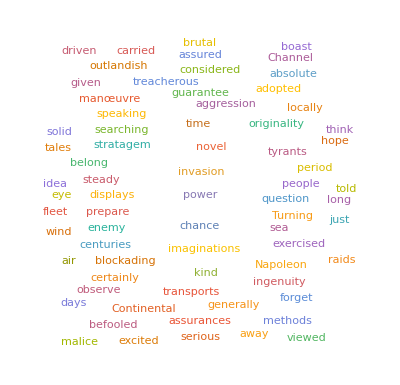

```mathematica
WordCloud[DeleteStopwords[ChurchillSpeech]]
```

### Task 23

Give 3 of the most frequently used words in the fragment. (Hint: Use the TextWords function)

```mathematica
Reverse[SortBy[Tally[TextWords[DeleteStopwords[ChurchillSpeech]]], Last]]
```

{{time,2},{power,2},{novel,2},{kind,2},{invasion,2},{chance,2},{wind,1},{viewed,1},{tyrants,1},{Turning,1},{treacherous,1},{transports,1},{told,1},{think,1},{tales,1},{stratagem,1},{steady,1},{speaking,1},{solid,1},{serious,1},{searching,1},{sea,1},{raids,1},{question,1},{prepare,1},{period,1},{people,1},{outlandish,1},{originality,1},{observe,1},{Napoleon,1},{methods,1},{manœuvre,1},{malice,1},{long,1},{locally,1},{just,1},{ingenuity,1},{imaginations,1},{idea,1},{hope,1},{guarantee,1},{given,1},{generally,1},{forget,1},{fleet,1},{eye,1},{exercised,1},{excited,1},{enemy,1},{driven,1},{displays,1},{days,1},{Continental,1},{considered,1},{Channel,1},{certainly,1},{centuries,1},{carried,1},{brutal,1},{boast,1},{blockading,1},{belong,1},{befooled,1},{away,1},{assured,1},{assurances,1},{air,1},{aggression,1},{adopted,1},{absolute,1}}

### Task 24

Use the speech text to train a sequence predictor using a Markov chain of order 2.

### Task 25

Use the trained predictor to predict the next word in the sentence “absolute guarantee against”. Does the result make sense?

### Task 26

Predict the most likely 4 elements completing the sentence “absolute guarantee against”.

### Task 27

Sort the words that complete the sentence “absolute guarantee against” in increasing order in terms of their probability.